```mathematica
datawf=Import["/home/daniel/Documents/Codigos/QuantumDynamics/wavefunction.dat"];
datawigner=Import["/home/daniel/Documents/Codigos/QuantumDynamics/wignerfunction.dat"];
```

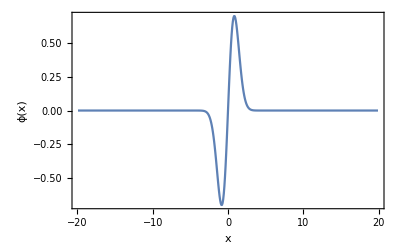

```mathematica
ListPlot[datawf,PlotRange->All,Frame->True,Joined->True,FrameLabel->{"x","ϕ(x)"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
wigner2=ListPlot3D[datawigner,PlotRange->{{-3,3},{-3,3},{-0.25,0.35}},AxesLabel->{"x","p","W"},LabelStyle->Directive[Bold,Medium]]
```

-Graphics3D-

```mathematica
wigner2=ListDensityPlot[datawigner,PlotRange->{{-3,3},{-3,3},All},Frame->True,FrameLabel->{"x","p"},LabelStyle->Directive[Bold,Medium],ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics-